```mathematica
Quit[];
```

```mathematica
s=NDSolve[{X'[t] == Y[t],
Y'[t]==Z[t],Z'[t]==2 Y[t]-6 X[t] Y[t],
X[0]==1,Y[0]==0,Z[0]==-1},{X[t],Y[t],Z[t]},{t,-3,3}]
```

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t],Z[t]→InterpolatingFunction[…][t]}}

```mathematica
Table[X[t]/.s,{t,-3,3}]
```

{{0.0558616},{0.210771},{0.62929},{1.},{0.62929},{0.210771},{0.0558616}}

```mathematica
Table[Y[t]/.s,{t,-3,3}]
```

{{0.0767616},{0.264806},{0.541855},{0.},{-0.541855},{-0.264806},{-0.0767616}}

```mathematica
Table[Z[t]/.s,{t,-3,3}]
```

{{0.102362},{0.288269},{0.0705617},{-1.},{0.0705617},{0.288269},{0.102362}}

```mathematica
Quit[];
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==Z[t],Z'[t]==2 Y[t],
X[0]==1,Y[0]==0,Z[0]==-1},{X[t],Y[t],Z[t]},{t,-3,3}]
```

{{X[t]→1/4 (6-ⅇ^(-√2 t)-ⅇ^(√2 t)),Y[t]→-(ⅇ^(-√2 t) (-1+ⅇ^(2 √2 t)))/(2 √2),Z[t]→-1/2 ⅇ^(-√2 t) (1+ⅇ^(2 √2 t))}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→1/2 (3-Cosh[√2 t]),Y[t]→-Sinh[√2 t]/(√2),Z[t]→-Cosh[√2 t]}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(Sech[t/√2])^2},{t,-1,1},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Green,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

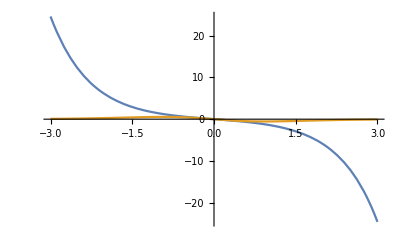

```mathematica
Plot[{Evaluate[Y[t]/.sol],-√2 Sech[t/(√2)]^2 Tanh[t/(√2)]},{t,-3,3},PlotRange->All]
```

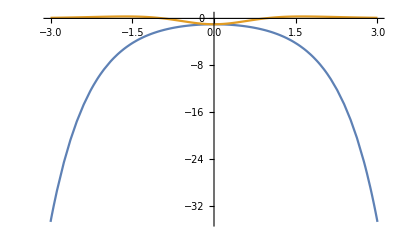

```mathematica
Plot[{Evaluate[Z[t]/.sol],-Sech[t/(√2)]^4+2 Sech[t/(√2)]^2 Tanh[t/(√2)]^2},{t,-3,3},PlotRange->All]
```

```mathematica
Quit[];
```

```mathematica
b[t_]:=(Sech[t/√2])^2;
```

```mathematica
D[b[t],t]
```

-√2 Sech[t/(√2)]^2 Tanh[t/(√2)]

```mathematica
bb[t_]:=-√2 Sech[t/(√2)]^2 Tanh[t/(√2)]  (*1D*)
```

```mathematica
D[bb[t],t]
```

-Sech[t/(√2)]^4+2 Sech[t/(√2)]^2 Tanh[t/(√2)]^2

```mathematica
bbb[t_]:=-Sech[t/(√2)]^4+2 Sech[t/(√2)]^2 Tanh[t/(√2)]^2; (*2D*)
```

```mathematica
D[bbb[t],t]
```

4 √2 Sech[t/(√2)]^4 Tanh[t/(√2)]-2 √2 Sech[t/(√2)]^2 Tanh[t/(√2)]^3

```mathematica
bbbb[t_]:=4 √2 Sech[t/(√2)]^4 Tanh[t/(√2)]-2 √2 Sech[t/(√2)]^2 Tanh[t/(√2)]^3; (*3D*)
```

```mathematica
bbbb[t]+6 b[t] bb[t]-2 bb[t]
```

2 √2 Sech[t/(√2)]^2 Tanh[t/(√2)]-2 √2 Sech[t/(√2)]^4 Tanh[t/(√2)]-2 √2 Sech[t/(√2)]^2 Tanh[t/(√2)]^3

```mathematica
Simplify[bbbb[t]+6 b[t] bb[t]-2 bb[t]]
```

0